```mathematica
<<peeters`

(*relative to ~/physicsplay*)
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

peeters`

/Users/pjoot/project/figures/GAelectrodynamics

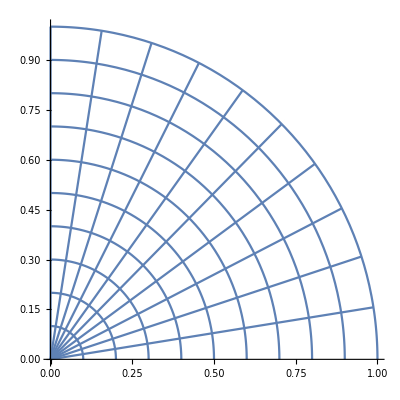

```mathematica
ClearAll[ toVector, polar]

toVector[z_] := {z // Re, z //Im};

polar[r_, t_] := r Exp[I t] // toVector;

Module[{t1,t2,tm, range},
range = {{0,1},{0,1}};
t1 = Table[ParametricPlot[polar[r,t],{t,0,Pi/2}, PlotRange-> range],{r,0.1,1,0.1}] ;
tm = Pi/2;
t2 = Table[ParametricPlot[polar[r,t],{r,0,1}, PlotRange->range],{t,0.1tm,tm,0.1tm}] ;
Show[t1,t2]
]
```

x

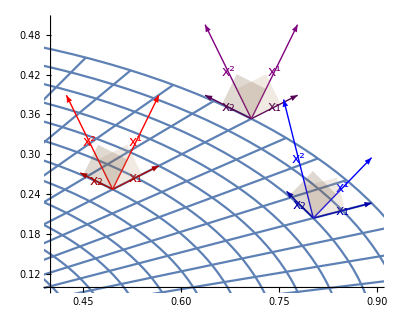

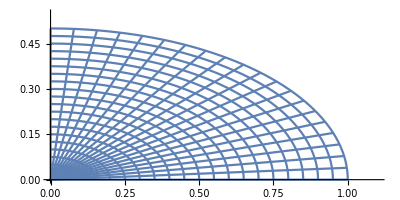

```mathematica
ClearAll[  (*elliptical,*)ellipticalH, x1, x2, r1, r2]

(*elliptical[a_, b_,t_] :=  Module[{m},
m = ArcTanh[b/a];
a Cosh[m+ I t]/Cosh[m] // toVector];*)

x1[a_,t_] :=  Module[{m},
m = ArcTanh[1/2];
 Cosh[m+ I t]/Cosh[m] // TrigExpand // toVector];
x2[a_,t_] :=  Module[{m},
m = ArcTanh[1/2];
 a I Sinh[m+ I t]/Cosh[m] // TrigExpand // toVector];
ellipticalH[a_,t_] := a x1[a,t];

r1[a_,t_] :=  Module[{m},
m = ArcTanh[1/2];
 2   Sinh[m+ I t]/Cosh[m] // TrigExpand// toVector];
r2[a_,t_] =  Module[{m},
m = ArcTanh[1/2];
 2 I Cosh[m+ I t]/Cosh[m]/a // TrigExpand // toVector];


boldx = Style["x", Bold]
boldsubx  = Style[Subscript[ boldx, #], FontSize-> 14, Background-> White] &;
boldsuperx  = Style[Superscript[ boldx, #], FontSize-> 14, Background-> White] &;

p2 = Module[{t1,t2,tm,range, p1, rp1, tp1, g, p2, rp2, tp2, da, rp3, tp3, p3,  dx11, dx21, dx12, dx22, dx13, dx23},
(*range =1.1 {{0,1},{0,1}};*)
range = {{0.4,0.9},{0.1,0.5}};
tm = Pi/2;
da = 0.1;

t1 = Table[ParametricPlot[ellipticalH[r,t],{t,0,tm}, PlotRange->range],{r,0.1,1,0.05}] ;
t2 = Table[ParametricPlot[ellipticalH[r,t],{r,0,1}, PlotRange->range],{t,0,tm,0.05tm}] ;
rp1 = 0.7;
tp1 = 5 Pi/20;
p1 = ellipticalH[rp1, tp1];
dx11 = da x1[rp1, tp1];
dx21 = da x2[rp1, tp1];
dr11 = da r1[rp1, tp1];
dr21 = da r2[rp1, tp1];


rp2 = 0.9;
tp2 = 3 Pi/20;
p2 = ellipticalH[rp2, tp2];
dx12 = da x1[rp2, tp2];
dx22 = da x2[rp2, tp2];
dr12=da r1[rp2,tp2];
dr22=da r2[rp2,tp2];

rp3=1.0;
tp3 = 5 Pi/20;
p3=ellipticalH[rp3,tp3];
dx13=da x1[rp3,tp3];
dx23=da x2[rp3,tp3];
dr13=da r1[rp3,tp3];
dr23=da r2[rp3,tp3];

g =Graphics[{
Red//Darker,
Thick,
Arrow[{p1, p1+dx11}],
Arrow[{p1, p1 + dx21}],
Text[ boldsubx[1], p1 + dx11/2],
Text[ boldsubx[2], p1 + dx21/2],
Thin,
Red,
Arrow[{p1, p1+dr11}],
Arrow[{p1, p1 + dr21}],
Text[ boldsuperx[1], p1 + dr11/2],
Text[ boldsuperx[2], p1 + dr21/2],
Thick,
Blue//Darker,
Arrow[{p2, p2+dx12}],
Arrow[{p2, p2 + dx22}],
Text[ boldsubx[1], p2 + dx12/2],
Text[ boldsubx[2], p2 + dx22/2],
Thin,
Blue,
Arrow[{p2, p2+dr12}],
Arrow[{p2, p2 + dr22}],
Text[ boldsuperx[1], p2 + dr12/2],
Text[ boldsuperx[2], p2 + dr22/2],
Thick,
Purple//Darker,
Arrow[{p3,p3+dx13}],
Arrow[{p3,p3+dx23}],
Text[ boldsubx[1], p3 + dx13/2],
Text[ boldsubx[2], p3 + dx23/2],
Thin,
Purple,
Arrow[{p3,p3+dr13}],
Arrow[{p3,p3+dr23}],
Text[ boldsuperx[1], p3 + dr13/2],
Text[ boldsuperx[2], p3 + dr23/2]



,Opacity[0.2]
,Brown//Lighter
,Parallelogram[p1,{dx11 // Normalize,dr21// Normalize}/20]
,Brown//Darker
,Parallelogram[p1,{dx21 // Normalize,dr11// Normalize}/20]

,Brown//Lighter
,Parallelogram[p2,{dx12//Normalize,dr22//Normalize}/20]
,Brown//Darker
,Parallelogram[p2,{dx22//Normalize,dr12//Normalize}/20]

,Brown//Lighter
,Parallelogram[p3,{dx13//Normalize,dr23//Normalize}/20]
,Brown//Darker
,Parallelogram[p3,{dx23//Normalize,dr13//Normalize}/20]


}];
Show[t1,t2, g]
]

p1 = Module[{t1,t2,tm,range, p1, rp1, tp1, g, dx11, dx21, p2, rp2, tp2, da, rp3, tp3, p3, dx13, dx23},
range =1.1 {{0,1},{0,0.5}};

tm = Pi/2;
da = 0.1;

t1 = Table[ParametricPlot[ellipticalH[r,t],{t,0,tm}, PlotRange->range],{r,0.05,1,0.05}] ;
t2 = Table[ParametricPlot[ellipticalH[r,t],{r,0,1}, PlotRange->range],{t,0,tm,0.05tm}] ;

Show[t1,t2]
]
```

```mathematica
(*peeters`exportForLatex["ellipticalContoursFig1", p1]*)
peeters`exportForLatex["ellipticalContoursFig2", p2]
```

{ellipticalContoursFig2.eps,ellipticalContoursFig2pn.png}

```mathematica
$Assumptions =  t > 0 && m > 0;
Simplify[Re[ Cosh[m - I t] Sinh[m + I t] /. m -> ArcTanh[1/2]]] 

r1[a,t].x1[a,t] // Simplify
r2[a,t].x2[a,t] // Simplify
r2[a,t].x1[a,t] // FullSimplify
r1[a,t].x2[a,t] // FullSimplify
```

2/3

1

1

0

0